# Efeito das Aproximações no Cálculo de Parâmetros para Cabos SC

## Antonio Carlos Siqueira de Lima Departamento de Engenharia Elétrica Universidade Federal do Rio de Janeiro acsl@dee.ufrj.br

## Opções de Projeto

```mathematica
Clear["Global`*"]
```

```mathematica
SetOptions[{ListPlot,ListLogLinearPlot,ListLogLogPlot},Frame->True,Axes->True,ImageSize->450,Joined->True,PlotStyle->{Thick}];
```

```mathematica
plstyle1={AbsoluteThickness[2],RGBColor[1,0,0], Hue[0]};
plstyle2={AbsoluteThickness[2],AbsoluteDashing[{5,0,5}],RGBColor[0,0,1]};
plstyle3={AbsoluteThickness[2],PointSize[.015],RGBColor[1,0,1]};
plstyle4={AbsoluteThickness[2],PointSize[.015],RGBColor[0,0,0]};
```

## Introdução

O objetivo deste arquivo é calcular os parâmetros unitários de um conjunto de cabos SC diretamente em coordenadas de fase. São utilizadas as expressões de Bessel para as impedâncias séries dos condutores, para o solo é considerada a representação do Wedepohl ao invés da formulação de Pollaczcek. O comprimento do cabo é de 10km

## Dados de entrada

Dimensões dos cabos

```mathematica
r1=1 10^-2;
r2=1.2 10^-2;
```

Constantes Elétricas e Parâmetros do Solo por metro

```mathematica
μ=4 π 10^-7;
ϵ=8.854 10^-12; 
ϵcs=3;
ϵg=10;
ϵ1=ϵcs ϵ;
ρc=3.365 10^-8;
ρ=100.0;
ηc=√((ⅉ  ω μ)/ρc);
σ=1/ρ;
w=(σ+(0.057849+ⅉ 0.12097)10^(-6) ω^0.71603);
k2=ω √(μ ϵ);
k1=√(ω^2 μ ϵ ϵg+I ω μ σ);
γg=Sqrt[I ω μ  (σ+I ω ϵ ϵg)];
η=I k1;
```

```mathematica
ℓ=10000;
```

## Desenho da rede

Espaçamento dos condutores

```mathematica
x1=0;
xc={x1,x1};
hc={1,1};
r={r1,r2};
```

```mathematica
mostra=Table[{Circle[{xc[[i]],-hc[[i]]},r[[i]]]},{i,1,2}];
```

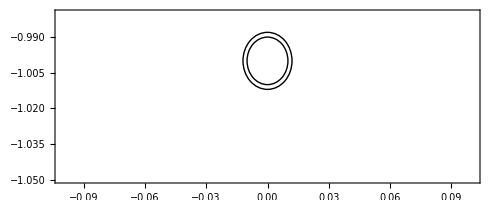

```mathematica
rr=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->True,PlotRange->{{-0.1,0.1},{-1.05,-.98}}]
```

```mathematica
de=√(r2^2+4 hc[[1]]^2);
```

## Frequências e listas

#### Faixa de Frequência

```mathematica
logspace[f1_,f2_,n_]:=Table[10^(f1+((f2-f1)/(n-1))*x),{x,0,n-1}]//N;
f=logspace[-2,8,120];
nf=Dimensions[f][[1]];
```

```mathematica
Max[f]
```

1.×10^8

Inicializando listas para o fator de propagação e para admitância característica

```mathematica
Yn=Table[0,{n,1,nf}];
eigAfase=Yn;
eigAfase2=Yn;
Yn2=Yn;
eigAfase3=Yn;
Yn3=Yn;
Zcabo=Yn;
Ycabo=Yn;
Ycabo2=Yn;
Ycabo3=Yn;
Ycabo4=Yn;
```

## Cálculo usando as formulação de Bessel & Pollaczek

```mathematica
int=10;
```

```mathematica
Timing[Do[{ω=2π f[[nm]],
(* Impedancias internas*)
z1=(ρc ηc)/(2π r1)BesselI[0,ηc r1]/BesselI[1,ηc r1],
z2=ⅉ(ω μ)/(2π)Log[r2/r1],
(* Impedancias externas*)

Js=2 NIntegrate[Exp[-2 hc[[1]] √(α^2+η^2)]/(Abs[α]+√(α^2+η^2))Cos[r2 α],{α,0,int},MaxRecursion->50],
(*z7=(ρ η^2)/(2 π)(BesselK[0,η r2]-BesselK[0,η de ]+Js),*)
(*z7=(ⅈ ω μ)/(2π)(BesselK[0,r2 η]+((4hc[[1]]^2-r2^2)  BesselK[2,η  de])/de^2-2 (4hc[[1]]^2-r2^2) Exp[-2hc[[1]] η]/(η^2 ( de^4))( 1+2hc[[1]] η )),,*)
(*z7=ⅉ(ω μ)/(2π)(-Log[(EulerGamma η r2)/2]+1/2-(4η)/3 hc[[1]]),*)
z7=(ⅉ ω μ)/(2 π) Log[(1+γg r2)/(γg r2)],
Zcabo[[nm]]={{z1+z2+z7}},

(*MODELO DE ADMITÂNCIA N° 01 - Modelo proposto*)
(* matrix de admitância externa*)
yc=(ⅉ ω 2 π ϵ1)/Log[r2/r1] ,
Jy3=NIntegrate[Exp[-2 hc[[1]] Sqrt[α^2+ η^2]]/(Abs[α]+ ((k2^2)/(k1^2))  Sqrt[α^2+ η^2])Cos[r2 α],{α,0,int},MaxRecursion->500],
λp3=BesselK[0,η r2]-BesselK[0,η de],
ys=(2 π (σ+I ω ϵ ϵg))/(λp3+2 Jy3) ,
(* montagem da matrix de admitância*)
Yintext0={{((yc ys)/(yc+ ys))}},
Ycabo[[nm]]=Yintext0,

(*MODELO DE ADMITÂNCIA N° 02 - Modelo usual*)
(* matrix de admitância interna*)
Yint={{yc}},
Ycabo2[[nm]]=Yint,

(*MODELO DE ADMITÂNCIA N° 03 - Petrache*)
Yg11=(γg^2)/z7(*Zpetr*),
cpc=(2 π ϵ1)/Log[r2/r1] ,
σi=10^-20,
gdg=σi/ϵ1 cpc,
yc2=gdg+I ω cpc,
Yintext={{((yc2 Yg11)/(yc2+ Yg11))}},
Ycabo3[[nm]]=Yintext,

Ycabo4[[nm]]={{Yg11}}


},{nm,1,nf}];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{46.754,Null}

```mathematica
Timing[Do[{ω=2π f[[nm]],
eval=Eigenvalues[N[Zcabo[[nm]].Ycabo[[nm]]]],
evect=Eigenvectors[N[Zcabo[[nm]].Ycabo[[nm]]]],
γ=Sqrt[eval],
Tv=Transpose[evect],
Tvi=Inverse[Transpose[evect]],
hm=Exp[-γ*ℓ],
eigAfase[[nm]]=hm,
den=(1-hm^2),
Am=γ*(1+hm^2)/den,
Bm=-2.0*γ*hm/den,
A=N[Inverse[Zcabo[[nm]]]].Tv.DiagonalMatrix[Am].Tvi,
B=N[Inverse[Zcabo[[nm]]]].Tv.DiagonalMatrix[Bm].Tvi,
Ynodal=ArrayFlatten[{{A,B},{B,A}}],
Yn[[nm]]=Eigenvalues[Ynodal]
},{nm,1,nf}];]
```

{0.125,Null}

```mathematica
Timing[Do[{ω=2π f[[nm]],
eval=Eigenvalues[N[Zcabo[[nm]].Ycabo2[[nm]]]],
evect=Eigenvectors[N[Zcabo[[nm]].Ycabo2[[nm]]]],
γ=Sqrt[eval],
Tv=Transpose[evect],
Tvi=Inverse[Transpose[evect]],
hm=Exp[-γ*ℓ],
eigAfase2[[nm]]=hm,
den=(1-hm^2),
Am=γ*(1+hm^2)/den,
Bm=-2.0*γ*hm/den,
A=N[Inverse[Zcabo[[nm]]]].Tv.DiagonalMatrix[Am].Tvi,
B=N[Inverse[Zcabo[[nm]]]].Tv.DiagonalMatrix[Bm].Tvi,
Ynodal=ArrayFlatten[{{A,B},{B,A}}],
Yn2[[nm]]=Eigenvalues[Ynodal]
},{nm,1,nf}];]
```

{0.156,Null}

```mathematica
Timing[Do[{ω=2π f[[nm]],
eval=Eigenvalues[N[Zcabo[[nm]].Ycabo3[[nm]]]],
evect=Eigenvectors[N[Zcabo[[nm]].Ycabo3[[nm]]]],
γ=Sqrt[eval],
Tv=Transpose[evect],
Tvi=Inverse[Transpose[evect]],
hm=Exp[-γ*ℓ],
eigAfase3[[nm]]=hm,
den=(1-hm^2),
Am=γ*(1+hm^2)/den,
Bm=-2.0*γ*hm/den,
A=N[Inverse[Zcabo[[nm]]]].Tv.DiagonalMatrix[Am].Tvi,
B=N[Inverse[Zcabo[[nm]]]].Tv.DiagonalMatrix[Bm].Tvi,
Ynodal=ArrayFlatten[{{A,B},{B,A}}],
Yn3[[nm]]=Eigenvalues[Ynodal]
},{nm,1,nf}];]
```

{0.109,Null}

## Conferindo

```mathematica
Ycabo[[120]]
Ycabo2[[120]]
Ycabo3[[120]]
Ycabo4[[120]]
```

{{0.0236832+0.0971089 ⅈ}}

{{0.575152 ⅈ}}

{{-0.0272386+0.0981521 ⅈ}}

{{-0.039473+0.116095 ⅈ}}

## Plotagens

```mathematica
SetOptions[{ListPlot,ListLogLinearPlot,ListLogLogPlot},Frame->True,ImageSize->750,Joined->True,PlotStyle->{Thick}];
```

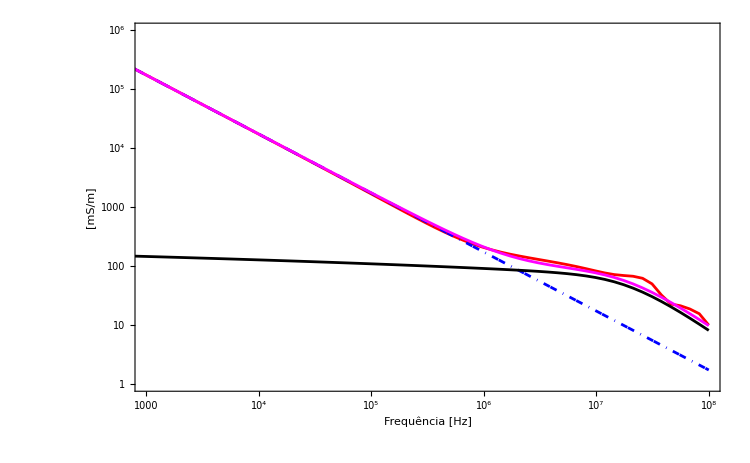

```mathematica
pcable01=ListLogLogPlot[Transpose[{f,1/Abs[Ycabo[[Range[nf],1,1]]]}], 
Joined->{True,False},
FrameLabel-> {"Frequência [Hz]","[mS/m]"},
BaseStyle->{Medium,FontFamily->"Helvetica"},PlotStyle->plstyle1,PlotRange->{{1000,10^8},{1,10^6}}];
pcable02=ListLogLogPlot[Transpose[{f,1/Abs[Ycabo2[[Range[nf],1,1]]]}], 
Joined->{True,False},
FrameLabel-> {"Frequência [Hz]","[mS/m]"},
BaseStyle->{Medium,FontFamily->"Helvetica"},PlotStyle->plstyle2];
pcable03=ListLogLogPlot[Transpose[{f,1/Abs[Ycabo3[[Range[nf],1,1]]]}], 
Joined->{True,False},
FrameLabel-> {"Frequência [Hz]","[mS/m]"},
BaseStyle->{Medium,FontFamily->"Helvetica"},PlotStyle->plstyle3];
pcable04=ListLogLogPlot[Transpose[{f,1/Abs[Ycabo4[[Range[nf],1,1]]]}], 
Joined->{True,False},
FrameLabel-> {"Frequência [Hz]","[mS/m]"},
BaseStyle->{Medium,FontFamily->"Helvetica"},PlotStyle->plstyle4,PlotRange->{{1000,10^8},{1,10^6}}];
ppp=Show[{pcable01,pcable02,pcable03,pcable04}]
```

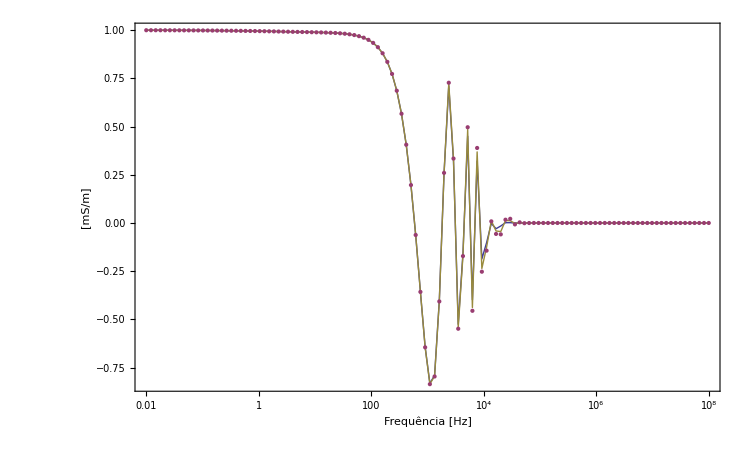

```mathematica
ListLogLinearPlot[{
Transpose@{f,Re[eigAfase[[All,1]] ]},
Transpose@{f,Re[eigAfase2[[All,1]] ]},
Transpose@{f,Re[eigAfase3[[All,1]] ]}}, 
Joined->{True,False},
FrameLabel-> {"Frequência [Hz]","[mS/m]"},
BaseStyle->{Medium,FontFamily->"Helvetica"}]
```

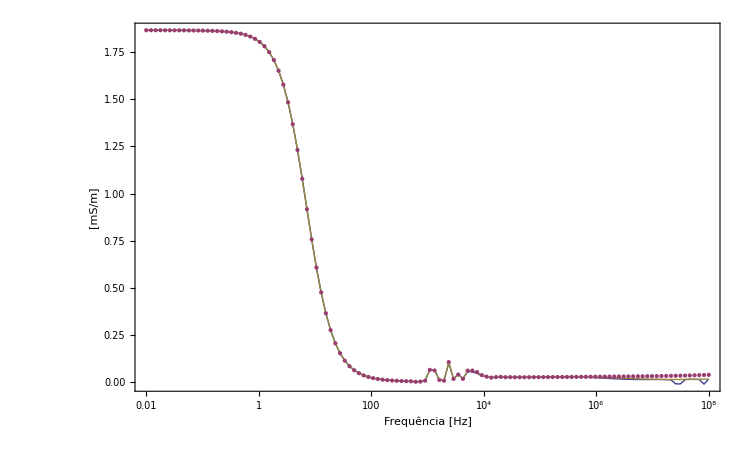

```mathematica
rrr2=ListLogLinearPlot[{
Transpose@{f,Re[Yn[[All,1]] ]},
Transpose@{f,Re[Yn2[[All,1]] ]},
Transpose@{f,Re[Yn3[[All,1]] ]}}, 
Joined->{True,False},
FrameLabel-> {"Frequência [Hz]","[mS/m]"},
BaseStyle->{Medium,FontFamily->"Helvetica"}]
```